```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls",
"load_takahashi_data.wl"
};
```

```mathematica
figureNameRepair="repair_in_light_and_dark";
figureDirectoryRepair=figureNameRepair;
```

```mathematica
parsRepairByLight[repairLight_]:=Join[{
L->Piecewise[{
{40,t<0},
{2000,t< 3600},
{0,t<1.5 3600},
{repairLight,True}
}],
tmin->-24 3600,
tmax->24 3600
},
pars[6]
];
```

```mathematica
repairLights={0,40};
dat["Repair"][40]=DeleteDuplicates@Normal@Select[data["Fig3B"],#"temp"==25.&][All,{3600(#["h"]+1.5)&,#["Fv/Fm"]&}];
```

```mathematica
dat["Repair"][0]=DeleteDuplicates@Normal@Select[data["FigS3"],#"temp"==25.&][All,{3600(#["h"]+1.5)&,#["Fv/Fm"]&}];
```

```mathematica
lightShadingColors={0->Lighter@Lighter@Gray,40->LightGreen,2000->LightRed};
```

```mathematica
timesRepairPlots={-.5 3600,5 3600};
```

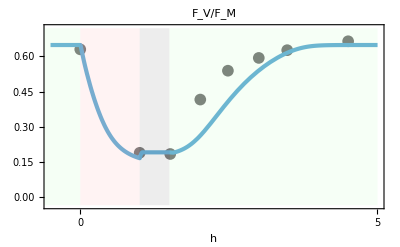
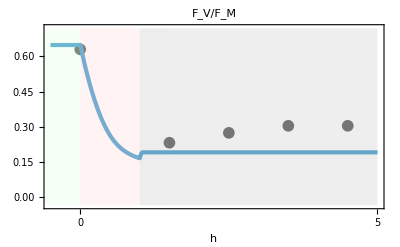
-Graphics--Graphics-Light
μmol quanta m^-2s^-1
40 | RGBColor[0.88, 1, 0.88]
2000 | RGBColor[1, 0.85, 0.85]
0 | RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778]

```mathematica
plotRepairByLight=Table[
Show[{ListPlot[dat["Repair"][repairLight],Joined->False,PlotMarkers->plotMarkers,PlotStyle->{Darker@Gray,Dashed,thickness},imageSizePadding[ImagePaddingXunits],FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks[[1;;-1;;1]],None}},
FrameLabel->{{None,None},{"h",None}},PlotRange->{timesRepairPlots,{FvFmMinPlot,FvFmMaxPlot}},Evaluate@style,PlotLabel->"F_V/F_M"],
plotSimulation[FvFm,parsRepairByLight[repairLight],timesRepairPlots,{Evaluate@imageSizePadding[ImagePaddingUnits],PlotRange->Full,FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks,None}}
}]},PlotRange->{{-.5,5}3600,{FvFmMinPlot,FvFmMaxPlot}},

Epilog->{
{40/.lightShadingColors,Opacity[0.3],Rectangle[{-1 3600,FvFmMinPlot},{0 3600,FvFmMaxPlot}]},
{2000/.lightShadingColors,Opacity[0.3],Rectangle[{0 3600,FvFmMinPlot},{1 3600,FvFmMaxPlot}]},
{0/.lightShadingColors,Opacity[0.3],Rectangle[{1 3600,FvFmMinPlot},{1.5 3600,FvFmMaxPlot}]},
{repairLight/.lightShadingColors,Opacity[0.289],Rectangle[{1.501 3600,FvFmMinPlot},{5 3600,FvFmMaxPlot}]},
Nothing
}],{repairLight,Reverse@repairLights}];
legendRepairByLight=Column[{Style["Light",FontFamily->font,14],Style[L/.units,FontFamily->font,14],Grid[Table[{Style[light,FontFamily->font,14],light/.lightShadingColors},{light,{40,2000,0}}],Alignment->Right]},Alignment->Center];
(Export[NotebookDirectory[]<>"export/simulations-repair-in-light-and-dark.pdf",#];#)&@Row[plotRepairByLight~Join~{Column[{legendRepairByLight,Spacer[{20,20}]}]}]
```

```mathematica
Table[Export[NotebookDirectory[]<>"export/"<>figureDirectoryRepair<>"/"<>figureNameRepair<>"-recovery-light="<>ToString[repairLight]<>".pdf",#]&@fullSimulationPanel[parsRepairByLight[repairLight],timesRepairPlots,{FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks[[1;;-1;;1]],None}}},{(FrameLabel->{{#/.units,None},{"h",None}})}&], {repairLight,repairLights}];
```